```mathematica
h = D1/2 - d + s/2;
```

```mathematica
L = 2 Sqrt[(D1/2)^2 - h^2]
```

2 √(D1^2/4-(-d+D1/2+s/2)^2)

```mathematica
FullSimplify[L]
```

√((2 d-s) (-2 d+2 D1+s))

```mathematica
Simplify[√(D1^2-(-2 d+D1+s)^2) ==√((2 d-s) (-2 d+2 D1+s)) ]
```

True

```mathematica
σL=FullSimplify[Simplify[D[ L,D1]]]
```

(2 d-s)/(√((2 d-s) (-2 d+2 D1+s)))

```mathematica
(*d: distanza_bordo, D: diametro, s: spessore2*)
(σL/.D1->316/.s->30/.d->50)//N
```

0.352924

```mathematica
f =(σL/.D1->316/.s->30)//N
```

(-30.+2. d)/(√((662.-2. d) (-30.+2. d)))

```mathematica
f/.d->30
```

0.223235

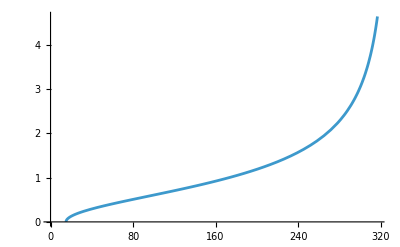

```mathematica
Plot[f,{d, 0, 317}]
```